```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:=150*x-100*x^2+0.3*x^4
```

```mathematica
xL=-20;
xR=20;
```

```mathematica
ConvexHullFunction[f_,a_,b_]:=Module[{top,g,R,poly,pickers,plist,pts},g=Plot[f[x],{x,a,b}];
pts=Join@@Cases[g,_Line,All][[All,1]];
top=Max[pts[[All,2]]];
R=ConvexHullMesh[Join[{{a,top+1}},pts,{{b,top+1}}]];
poly=MeshCells[R,2][[1,1]];
pickers=Range[MeshCellCount[R,0]] UnitStep[Subtract[top+0.5,MeshCoordinates[R][[All,2]]]];
plist=DeleteCases[pickers[[poly]],0];
pts=SortBy[MeshCoordinates[R][[plist]],First];
Interpolation[pts,InterpolationOrder->1]]
```

```mathematica
g=ConvexHullFunction[f,xL,xR];
```

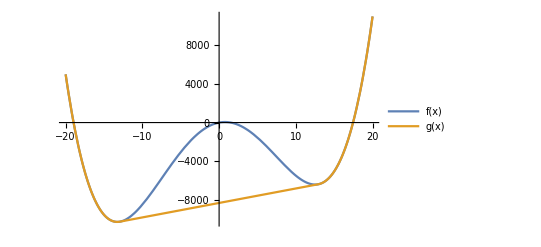

```mathematica
plot=Plot[{f[x],g[x]},{x,xL,xR},PlotLegends->"Expressions"]
```

```mathematica
G[x_,CL_,u1_,u2_,x1_,CR_]:=Piecewise[{{1/2*CL*x^2+(u2-u1)/x1*x+u1,x<=0},{u1+(u2-u1)/x1*x,0<x<x1}},1/2*CR*(x-x1)^2+((u2-u1)/x1)*(x-x1)+u2](*{{1/2*Subscript[C, L]*x^2+u1,x<=0},{u1+(u2-u1)/x1*x,0<x<x1}},1/2*Subscript[C, R]*(x-x1)^2+u2*)
```

```mathematica
Manipulate[Plot[G[x,CL,u1,u2,x1,CR],{x,-20,20},PlotRange->{0,200}],{CL,1,2},{u1,0,20},{u2,0,30},{x1,1,10},{CR,1,2}]
```

```mathematica
F[x_,y_,CL_,u1_,u2_,x1_,CR_]:=G[x,CL,u1,u2,x1,CR]*y^2
```

```mathematica
Manipulate[Plot3D[F[x,y,CL,u1,u2,x1,CR],{x,-20,20},{y,-10,10},PlotRange->{-20000,20000}],{CL,1,2},{u1,0,2000},{u2,2000,3000},{x1,1,10},{CR,1,2}]
```

```mathematica
Manipulate[NMinimize[F[x,y,CL,u1,u2,x1,CR],{x,y}],{CL,1,2},{u1,1,2},{u2,2,3},{x1,1,3},{CR,1,2}]
```

```mathematica
Ans[CL_,u1_,u2_,x1_,CR_,s_]:=Minimize[F[x,y,CL,u1,u2,x1,CR]-s*(x-y),{x,y}]
```

```mathematica
Minimize[F[x,y,CL,u1,u2,x1,CR]-s*(x-y),{x,y}]
```

Minimize[-s (x-y)+y^2 (Piecewise[{{u1+(CL x^2)/2+((-u1+u2) x)/x1, x≤0}, {u1+((-u1+u2) x)/x1, 0<x<x1}, {u2+1/2 CR (x-x1)^2+((-u1+u2) (x-x1))/x1, True}}]),{x,y}]

```mathematica
Manipulate[NMinimize[F[x,y,CL,u1,u2,x1,CR]-s*(x-y)/Sqrt[2],{x,y}],{CL,1,2},{u1,1,2},{u2,2,3},{x1,1,3},{CR,1,2},{s,0,10}]
```

```mathematica
h1[x_]:=Piecewise[{{1/2*1*x^2+(30-15)/10*x+15,x<=0},{15+(30-15)/10*x,0<x<10}},1/2*1*(x-10)^2+((30-15)/10)*(x-10)+30]
```

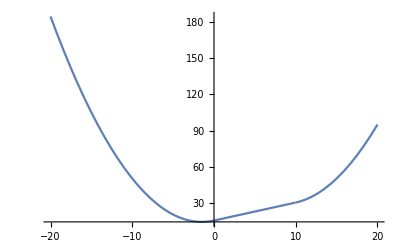

```mathematica
Plot[h1[x],{x,-20,20}]
```

```mathematica
Manipulate[{NMinimize[h1[x]-s*x,{x}][[1]]-h1[ArgMin[h1[x]-s*x,{x}][[1]]]-s*ArgMin[h1[x]-s*x,{x}][[1]]},{s,0,10}]
```

```mathematica
Manipulate[{ArgMin[h1[x]-s*x,{x}][[1]],h1[ArgMin[h1[x]-s*x,{x}][[1]]]-s*ArgMin[h1[x]-s*x,{x}][[1]]},{s,0,10}]//N
```

```mathematica
Manipulate[NMinimize[h1[x]-s*x,{x}],{s,0,10}]
```

```mathematica
h1[15.5]-7*15.5
```

-55.125

```mathematica
(*Manipulate[Plot[{h1[x],s*(x-ArgMin[h1[x]-s*x,{x}])+h1[NMinimize[h1[x]-s*x,{x}][[1]]]},{x,Subscript[x, min],Subscript[x, max]}],{s,0,10}]*)
```

```mathematica
H[x_,y_]:=h1[x]*y^2
```

```mathematica
Plot3D[H[x,y],{x,-20,20},{y,-10,10},PlotRange->{0,10000}]
```

-Graphics3D-

```mathematica
Manipulate[NMinimize[H[x,y]-s*(x-y),{x,y}],{s,-10,10}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

```mathematica
(*We minimize each portion separately with constraint, then select the min among them*)
```

```mathematica
g1[x_,y_]:=(1/2*1*x^2+(30-15)/10*x+15)*y^2
```

```mathematica
g2[x_,y_]:=(15+(30-15)/10*x)*y^2
```

```mathematica
g3[x_,y_]:=(1/2*1*(x-10)^2+((30-15)/10)*(x-10)+30)*y^2
```

```mathematica
Manipulate[NMinimize[{g1[x,y]-s*(x-y),},{x,y}],{s,-10,10}]
```

NMinimize::bcons: The following constraints are not valid: {Null}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

```mathematica
Plot3D[(1/2*1*x^2+(30-15)/10*x+15)*y^2,{x,-20,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Manipulate[NMinimize[{(1/2*1*x^2+(30-15)/10*x+15)*y^2-s*(x-y),x<=0},{x,y}],{s,-10,10}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.